```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.3;
ωmax=3.7;
Amin=0.0;
Amax=0.08;
Npoints=100;
M=32;
M2=3;
κ=1;
η=0.1;
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-0.45)/(0.7-0.45)]]
cf[x_]:=Lighter[Red]
```

/Users/zack/Documents/oscillators/pendulum

```mathematica
Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]]
Mean[Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]]^2]^(1/2)
Mean[Riffle[ConstantArray[0.5,8],ConstantArray[-0.5,8]]^2]^(1/2)
```

{0.562508,-0.511741,0.37669,-0.688886,0.306457,-0.498725,0.575321,-0.4382,0.482389,-0.492157,0.241089,-0.682259,0.552114,-0.699509,0.563754,-0.357587,0.291096,-0.543448,0.383693,-0.452996,0.569827,-0.636375,0.309392,-0.666294,0.290257,-0.273751,0.468473,-0.636087,0.620352,-0.472238,0.29066,-0.473081}

0.5

0.5

```mathematica
Flatten[Import["data/newrandom/randomlengths"<>ToString[10]<>".dat"]]
Mean[Flatten[Import["data/newrandom/randomlengths"<>ToString[10]<>".dat"]]^2]^(1/2)
Mean[Riffle[ConstantArray[0.5,8],ConstantArray[-0.5,8]]^2]^(1/2)
```

Import::nffil: File data/newrandom/randomlengths10.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Flatten[$Failed]

Import::nffil: File data/newrandom/randomlengths10.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

√Mean[Flatten[$Failed]^2]

0.5

```mathematica
Mean[Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]]-Mean[Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]]]]
Mean[(Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]]-Mean[Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]]])^2]^(1/2)
```

5.20417×10^-18

0.497369

## Equations

```mathematica
Clear[κ]
Clear[η]
Clear[L]
xhat={1,0};
zhat={0,1};
A[i_,j_]:={0,a*m}
a=γ*L0*ω^2;
g=L0;
m=1;
x[i_,j_,t_]:={L[i]*Sin[θ[i][t]],-L[i]*Cos[θ[i][t]]}
Δ[i_,j_,t_]:=(-m*g*zhat+κ*((x[i+1,j,t]+δ*xhat+(L[i+1]-L[i])*zhat-(x[i,j,t]))+(x[i-1,j,t]-δ*xhat+(L[i-1]-L[i])*zhat-(x[i,j,t])))+A[i,j]*Cos[t]+T*x[i,j,t]);
eqn=FullSimplify[{Cos[θ[i][t]],Sin[θ[i][t]]}.(m*ω^2*D[x[i,j,t],{t,2}]-Δ[i,j,t]+η*ω*D[x[i,j,t],t])/(L0*m)]
κ=1;
η=0.1;
```

1/L0((L0-L0 γ ω^2 Cos[t]-κ L[1+i]) Sin[θ[i][t]]-κ L[-1+i] (Sin[θ[-1+i][t]-θ[i][t]]+Sin[θ[i][t]])+κ L[1+i] Sin[θ[i][t]-θ[1+i][t]]+L[i] (2 κ Sin[θ[i][t]]+η ω θ[i]'[t]+ω^2 θ[i]''[t]))

## Direct simulations

```mathematica
rate2[γ_,ω_,lengths_]:=
Module[{tmax,dt,t1,pbcs,eqns,ics,sol,norms,maxes,θ,t,Δ,fourier,q0,β,freq},
Δ[i_]:=lengths[[Mod[i-1,M]+1]];
tmax=2*Pi*100;
t1=2*Pi*50;
dt=2*Pi*0.05;
pbcs={θ[0]->θ[M],θ[M+1]->θ[1]};
eqns=Table[0==(1+ 2*κ (1+Δ[i])-γ ω^2 Cos[t]) θ[i][t]-κ θ[-1+i][t] (1+Δ[-1+i])-κ θ[1+i][t] (1+Δ[1+i])+(1+Δ[i]) (η ω θ[i]'[t]+ω^2 θ[i]''[t])/.pbcs,{i,1,M}];
ics=Join[Table[θ[i][0]==Sum[10^-3*(Sin[q*i]+Cos[q*i]),{q,0,Pi,2*Pi/M}],{i,1,M}],Table[θ[i]'[0]==0,{i,1,M}]];
sol=NDSolve[{eqns,ics},Table[θ[i],{i,1,M}],{t,0,tmax}];
norms=Table[Sum[Abs[θ[i][t]]^2,{i,1,M}]/M/.sol[[1]],{t,t1,tmax,dt}];
If[MemberQ[Differences[Sign[Differences[norms]]],-2],
maxes=1+First/@Position[Differences[Sign[Differences[norms]]],-2];
fourier=Abs[Fourier[Table[(θ[i]/.sol[[1]])[maxes[[-1]]*dt],{i,1,M}]]][[1;;M/2+1]];
q0=(First@FirstPosition[fourier,Max[fourier]]-1)*2*Pi/M;
β=D[Fit[Transpose[{dt*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x];
freq=N[Max[{#,1-#}]&@((First@FirstPosition[#,Max[#]]-1)/((tmax-t1)/(2*Pi))&@Mean[Table[Abs[Fourier[Table[(θ[i][t]/.sol[[1]])/Exp[β/2*t],{t,t1,tmax,dt}]]][[1;;Round[(tmax-t1)/dt/2]]],{i,1,M}]])];
{q0,γ,ω,freq,If[norms[[maxes[[-1]]]] > norms[[maxes[[1]]]],β,-1],Transpose[{dt*Range[Length[norms]]/(2*Pi),Log[Abs[norms]]/Log[10]}],Transpose[{dt*maxes/(2*Pi),Log[Abs[norms[[maxes]]]]/Log[10]}],Table[θ[i]/.sol[[1]],{i,1,M}]},{0,γ,ω,1/(dt/(Pi)*Mean[Differences[maxes]]),-1,Transpose[{dt*Range[Length[norms]]/(2*Pi),Log[Abs[norms]]/Log[10]}],Transpose[{dt*Range[Length[norms]]/(2*Pi),Log[Abs[norms]]/Log[10]}],Table[θ[i]/.sol[[1]],{i,1,M}]}]]
```

{0.519018,Null}

{π/2,0.05,3.5,0.5,0.0206288}

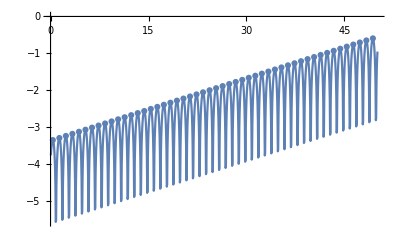

```mathematica
lengths=ConstantArray[0,M];
AbsoluteTiming[{q0,γ0,ω0,f0,β,norms,maxes,sol}=rate2[0.05,3.5,lengths];]
{q0,γ0,ω0,f0,β}
Show[ListPlot[norms,Joined->True,PlotRange->All],ListPlot[maxes,Joined->False,PlotRange->All]]
```

{0.494885,Null}

{π/2,0.06,3.5,0.5,0.0165444}

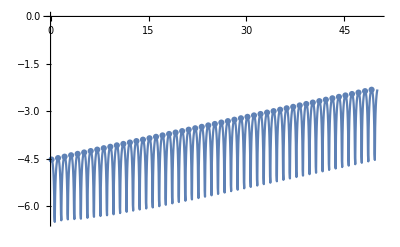

```mathematica
lengths=Flatten[Import["data/randomlengths/randomlengths"<>ToString[2]<>".dat"]];
lengths=Riffle[ConstantArray[0.35,M/2],ConstantArray[-0.35,M/2]];
AbsoluteTiming[{q0,γ0,ω0,f0,β,norms,maxes,sol}=rate2[0.06,3.5,lengths];]
{q0,γ0,ω0,f0,β}
Show[ListPlot[norms,Joined->True,PlotRange->All],ListPlot[maxes,Joined->False,PlotRange->All]]
```

```mathematica
lengths=ConstantArray[0,M];
AbsoluteTiming[Monitor[tongues1=Flatten[Table[ParallelTable[Quiet[rate2[γ,ω,lengths]][[1;;5]],{γ,Amin,Amax,(Amax-Amin)/Npoints}],{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}],1];,N[{(ω-ωmin)/(ωmax-ωmin)}]]]
Export["tongues1.dat",N[tongues1]]
```

{372.102,Null}

tongues1.dat

```mathematica
Δ=0.35;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
AbsoluteTiming[Monitor[tongues2=Flatten[Table[ParallelTable[Quiet[rate2[γ,ω,lengths]][[1;;5]],{γ,Amin,Amax,(Amax-Amin)/Npoints}],{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}],1];,N[{(ω-ωmin)/(ωmax-ωmin)}]]]
Export["tongues2.dat",N[tongues2]]
lengths=Δ/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
AbsoluteTiming[Monitor[tongues3=Flatten[Table[ParallelTable[Quiet[rate2[γ,ω,lengths]][[1;;5]],{γ,Amin,Amax,(Amax-Amin)/Npoints}],{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}],1];,N[{(ω-ωmin)/(ωmax-ωmin)}]]]1
Export["tongues3.dat",N[tongues3]]
```

{374.764,Null}

tongues2.dat

{378.853,Null}

tongues3.dat

```mathematica
Δ=0.5;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
AbsoluteTiming[Monitor[tongues5=Flatten[Table[ParallelTable[Quiet[rate2[γ,ω,lengths]][[1;;5]],{γ,Amin,Amax,(Amax-Amin)/Npoints}],{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}],1];,N[{(ω-ωmin)/(ωmax-ωmin)}]]]
Export["tongues5.dat",N[tongues5]]
```

{383.943,Null}

tongues5.dat

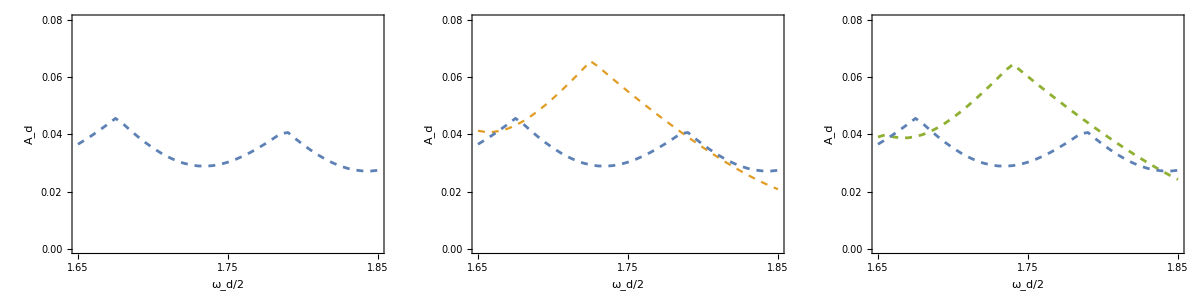

```mathematica
tongues1=Import["tongues1.dat"];
tongues2=Import["tongues2.dat"];
tongues3=Import["tongues3.dat"];
boundary1=Import["boundary1.dat"];
boundary2=Import["boundary2.dat"];
boundary3=Import["boundary3.dat"];
p1=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues1}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]];
p2=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues2}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary2,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],Dashed]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]];
p3=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues3}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary3,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[3]],Dashed,AbsoluteThickness[2]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]];
Grid[{{p1,p2,p3}}]
```

```mathematica
tongues5[[1]]
```

{tongues2}

0.56

```mathematica
tongues5=Import["tongues5.dat"];
cmin=Min[Cases[tongues5[[All,4]],u_/;u>0.51]];
cmax=Max[Cases[tongues5[[All,4]],u_/;u>0.51]];
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-cmin)/(cmax-cmin)]]
p1=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues5}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]]]
```

-Graphics-

```mathematica
Table[{i,PaddedForm[cmin+i*(cmax-cmin)/100,{3,2}]},{i,1,101,25}]
```

{{1, 0.56},{26, 0.60},{51, 0.63},{76, 0.67},{101, 0.70}}

```mathematica
{{1,cmin+0*(cmax-cmin)/100},{25,cmin+25*(cmax-cmin)/100},{50,50*(cmax-cmin)/100},{75,75*(cmax-cmin)/100},{100,100*(cmax-cmin)/100}}
```

{{1,0.56},{25,0.595},{50,0.07},{75,0.105},{100,0.14}}

```mathematica
p=MatrixPlot[Table[cf[(x-cmin)/(cmax-cmin)],{x,cmin,cmax,(cmax-cmin)/101},{j,1,10}],PlotRangePadding->None,FrameTicks->{{None,Table[{i,PaddedForm[cmin+i*(cmax-cmin)/100,{3,2}]},{i,0,100,25}]},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->20,ImageSize->60,PlotLabel->DisplayForm[RowBox[{"ω","/",Subscript["ω",d]}]],PlotRange->{{0,100},{1,10}},DataReversed->{True,False}]
Export["colorbar2.pdf",p]
```

-Graphics-

colorbar2.pdf

## Linear dispersion and candidate random cases

```mathematica
tongues1=Import["data/tongues1.dat"];
tongues2=Import["data/tongues2.dat"];
tongues3=Import["data/tongues3.dat"];
```

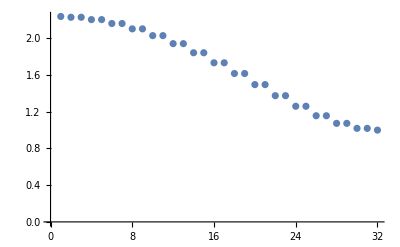

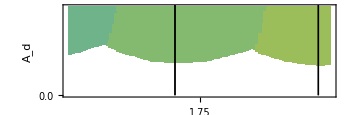

0.390181

frequencies1.dat

```mathematica
L0=1;
g=1;
lengths=ConstantArray[0,M];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
ListPlot[(4*#-η^2)^(1/2)/2&/@evals]
frequencies1=(4*#-η^2)^(1/2)/2&/@evals;

ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[1]]},{val[[3]],val[[2]],-1}],{val,tongues1}],InterpolationOrder->0,PlotRange->{All,All,{0,2*Pi}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/Pi]&),ColorFunctionScaling->False,FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,2.0,0.5}],Table[{i,""},{i,0,2.0,0.5}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.5,0.5}],Table[{i,""},{i,1.5,4.5,0.5}]}},RotateLabel->False, AspectRatio->1/3,ImagePadding->{{65,15},{65,10}},Epilog->(Line[{{2*#,0},{2*#,1}}]&/@frequencies1)]
Max[Differences[Sort[evals][[1;;M/2+5]]]]
Export["frequencies1.dat",frequencies1]
```

```mathematica
Δ=0.35;
L0=1;
g=1;
M=32;
κ=1;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
frequencies2=(4*#-η^2)^(1/2)/2&/@evals;
Export["frequencies2.dat",frequencies2]
```

frequencies2.dat

{0.130984,Null}

{0.851452,0.797721,10}

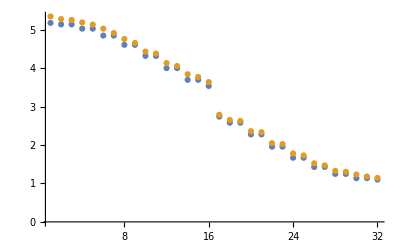

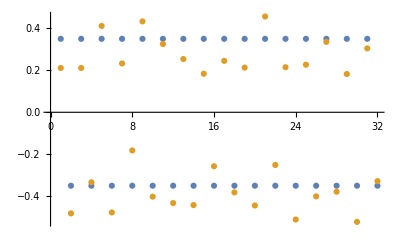

frequencies3.dat

```mathematica
Δ=0.35;
L0=1;
g=1;
M=32;
κ=1;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
trials={};
AbsoluteTiming[Monitor[Do[
maxlengths=Δ/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[n]<>".dat"]];
If[Min[maxlengths]>-0.9*L0,
mat=Table[(2*κ*(L0+maxlengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+maxlengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+maxlengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+maxlengths];
{maxevals,maxevecs}=Eigensystem[N[{mat,B}]];
AppendTo[trials,{Max[Differences[Sort[maxevals][[1;;M/2+5]]]],maxevals,maxevecs,maxlengths}];],{n,1,10}];,n]]
{max,maxevals,maxevecs,maxlengths}=First@MaximalBy[trials,#[[1]]&];
{max,maxevals,maxevecs,maxlengths}=trials[[9]];
{max,Max[Differences[Sort[evals][[1;;M/2+5]]]],Length[trials]}
ListPlot[{evals,maxevals},PlotRange->All]
ListPlot[{lengths,maxlengths}]
frequencies3=(4*#-η^2)^(1/2)/2&/@maxevals;
Export["frequencies3.dat",frequencies3]
```

{94.3521,Null}

{0.963877,0.797721,10000}

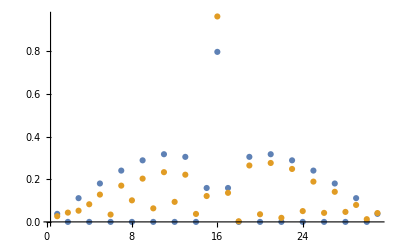

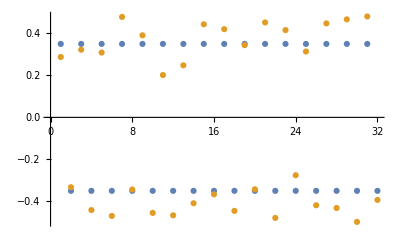

```mathematica
Δ=0.35;
L0=1;
g=1;
M=32;
κ=1;
time0=AbsoluteTime[];
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
frequencies=(4*#-η^2)^(1/2)/2&/@evals;
trials={};
n0=1*10^6;
nmax=10^4;
ϵ=0.5;
Δ2=Δ/(1+ϵ^2/3)^(1/2);
AbsoluteTiming[Monitor[Do[time=AbsoluteTime[];
SeedRandom[n0+n];
maxlengths=Riffle[ConstantArray[Δ2,M/2],ConstantArray[-Δ2,M/2]]+RandomReal[{-ϵ*Δ2,ϵ*Δ2},M];
mat=Table[(2*κ*(L0+maxlengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+maxlengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+maxlengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+maxlengths];
{maxevals,maxevecs}=Eigensystem[N[{mat,B}]];
AppendTo[trials,{Max[Differences[Sort[maxevals][[1;;M/2+1]]]],maxevals,maxevecs,maxlengths}];,{n,1,nmax}];,N[PaddedForm[{n/nmax, time-time0,(time-time0)*(1-n/nmax)/(n/nmax)} ,{6,6}]]]]
{max,maxevals,maxevecs,maxlengths}=First@MaximalBy[trials,#[[1]]&];
{max,Max[Differences[Sort[evals][[1;;M/2+1]]]],Length[trials]}
ListPlot[{Abs[Differences[evals]],Abs[Differences[maxevals]]},PlotRange->All]
ListPlot[{lengths,maxlengths}]
list=Reverse[SortBy[trials,#[[1]]&]][[1;;10,4]];
If[!DirectoryQ["data/newrandom/"],CreateDirectory["data/newrandom/"]];
Do[Export["data/newrandom/randomlengths"<>ToString[i]<>".dat", list[[i]]],{i,1,Length[list]}]
NotebookSave[]
```

```mathematica
Mean[list[[1]]]
Mean[list[[1]]^2]^(1/2)/Δ
Max[Abs[Differences[maxevals]]]
Max[Abs[Differences[evals]]]
```

-0.0170797

1.14499

0.963877

0.797721

{14270.,Null}

{0.792792,0.797721,1000000}

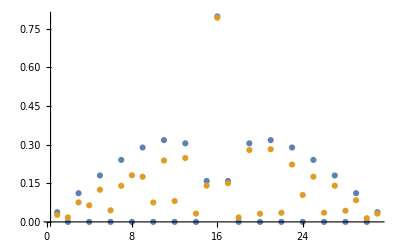

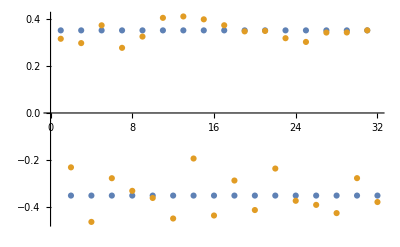

```mathematica
(* If we enforce the finite size heterogeneity scale and length constraints strictly, it is hard to improve on the periodic *)
Δ=0.35;
L0=1;
g=1;
M=32;
κ=1;
time0=AbsoluteTime[];
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
frequencies=(4*#-η^2)^(1/2)/2&/@evals;
trials={};
n0=5*10^6;
nmax=10^6;
ϵ=0.5;
Δ2=Δ/(1+ϵ^2/3)^(1/2);
AbsoluteTiming[Monitor[Do[time=AbsoluteTime[];
SeedRandom[n0+n];
maxlengths=Riffle[ConstantArray[Δ2,M/2],ConstantArray[-Δ2,M/2]]+RandomReal[{-ϵ*Δ2,ϵ*Δ2},M];
maxlengths=maxlengths-Mean[maxlengths];
maxlengths=Δ/Mean[maxlengths^2]^(1/2)*maxlengths;
mat=Table[(2*κ*(L0+maxlengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+maxlengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+maxlengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+maxlengths];
{maxevals,maxevecs}=Eigensystem[N[{mat,B}]];
AppendTo[trials,{Max[Differences[Sort[maxevals][[1;;M/2+1]]]],maxevals,maxevecs,maxlengths}];,{n,1,nmax}];,N[PaddedForm[{n/nmax, time-time0,(time-time0)*(1-n/nmax)/(n/nmax)} ,{6,6}]]]]
{max,maxevals,maxevecs,maxlengths}=First@MaximalBy[trials,#[[1]]&];
{max,Max[Differences[Sort[evals][[1;;M/2+1]]]],Length[trials]}
ListPlot[{Abs[Differences[evals]],Abs[Differences[maxevals]]},PlotRange->All]
ListPlot[{lengths,maxlengths}]
list=Reverse[SortBy[trials,#[[1]]&]][[1;;10,4]];
If[!DirectoryQ["data/strictrandom/"],CreateDirectory["data/strictrandom/"]];
Do[Export["data/strictrandom/randomlengths"<>ToString[i]<>".dat", list[[i]]],{i,1,Length[list]}]
NotebookSave[]
```

{96.2664,Null}

{0.870303,0.797721,10000}

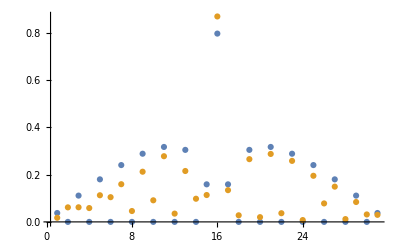

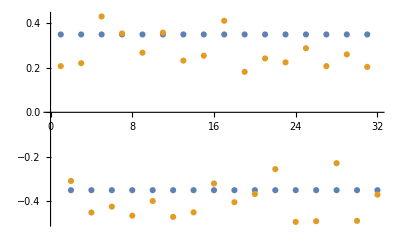

```mathematica
(* If we only enforce the finite size heterogeneity scale constraints strictly, it is possible to improve on the periodic *)
Δ=0.35;
L0=1;
g=1;
M=32;
κ=1;
time0=AbsoluteTime[];
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
mat=Table[(2*κ*(L0+lengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+lengths];
{evals,evecs}=Eigensystem[N[{mat,B}]];
frequencies=(4*#-η^2)^(1/2)/2&/@evals;
trials={};
n0=5*10^6;
nmax=10^4;
ϵ=0.5;
Δ2=Δ/(1+ϵ^2/3)^(1/2);
AbsoluteTiming[Monitor[Do[time=AbsoluteTime[];
SeedRandom[n0+n];
maxlengths=Riffle[ConstantArray[Δ2,M/2],ConstantArray[-Δ2,M/2]]+RandomReal[{-ϵ*Δ2,ϵ*Δ2},M];
maxlengths=Δ/Mean[maxlengths^2]^(1/2)*maxlengths;
mat=Table[(2*κ*(L0+maxlengths[[i]])+g)*KroneckerDelta[i,j]-κ*(L0+maxlengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]-κ*(L0+maxlengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j],{i,1,M},{j,1,M}];
B=DiagonalMatrix[L0+maxlengths];
{maxevals,maxevecs}=Eigensystem[N[{mat,B}]];
AppendTo[trials,{Max[Differences[Sort[maxevals][[1;;M/2+1]]]],maxevals,maxevecs,maxlengths}];,{n,1,nmax}];,N[PaddedForm[{n/nmax, time-time0,(time-time0)*(1-n/nmax)/(n/nmax)} ,{6,6}]]]]
{max,maxevals,maxevecs,maxlengths}=First@MaximalBy[trials,#[[1]]&];
{max,Max[Differences[Sort[evals][[1;;M/2+1]]]],Length[trials]}
ListPlot[{Abs[Differences[evals]],Abs[Differences[maxevals]]},PlotRange->All]
ListPlot[{lengths,maxlengths}]
list=Reverse[SortBy[trials,#[[1]]&]][[1;;10,4]];
If[!DirectoryQ["data/strictrandom/"],CreateDirectory["data/strictrandom/"]];
Do[Export["data/strictrandom/randomlengths"<>ToString[i]<>".dat", list[[i]]],{i,1,Length[list]}]
NotebookSave[]
```

```mathematica
list=Reverse[SortBy[trials,#[[1]]&]][[1;;10,4]];
Do[Export["data/randomlengths/randomlengths"<>ToString[i]<>".dat", list[[i]]],{i,1,Length[list]}]
```

## Inhomogeneous Floquet

```mathematica
mat1[s_,ω_,lengths_]:=ArrayFlatten[Table[((1+lengths[[i]])*(-ω^2*(s+n)^2+I*ω*η*(s+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1+lengths[[Mod[i-1+1,M]+1]])*KroneckerDelta[Mod[i-1+1,M]+1,j]*KroneckerDelta[n,m]-κ*(1+lengths[[Mod[i-1-1,M]+1]])*KroneckerDelta[Mod[i-1-1,M]+1,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,M},{j,1,M}]];
mat2[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,M},{j,1,M}]];
```

{71.5991,Null}

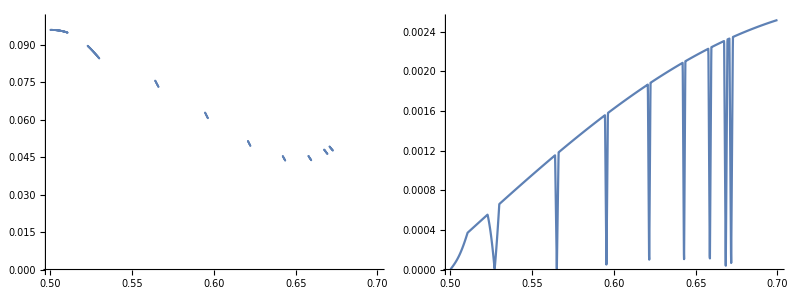

{0,69,91,94,96,98,100,102,104,106}

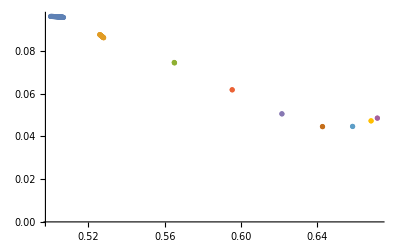

{{0.5238,0.5301},{0.5648,0.5654},{0.5953,0.5956},{0.6214,0.6217},{0.6427,0.643},{0.6585,0.6588},{0.6682,0.6685},{0.6715,0.6718}}

{1.69177,Null}

boundary5.dat

{284.147,Null}

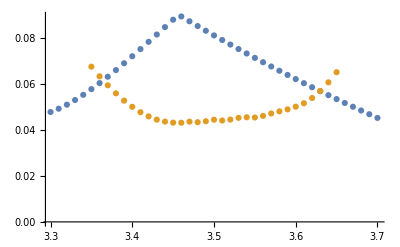

anharmonicboundary5.dat

```mathematica
Δ=0.5;
ω=3.5;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
AbsoluteTiming[vals=ParallelTable[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,lengths],mat2[ω]}];{eval,evec}=First@MinimalBy[DeleteCases[Transpose[{evals,evecs}],u_/;u[[1]]==ComplexInfinity],Abs[Im[#[[1]]]]&];
{ϵ,Re[eval],Im[eval],evec},{ϵ,0.5001,0.7,0.0001}];]

Grid[{{ListPlot[Abs[vals[[All,{1,2}]]],ImageSize->300,PlotRange->{0,0.1}],ListPlot[Abs[vals[[All,{1,3}]]],ImageSize->300,Joined->True,PlotRange->All]}}]
spikes=Cases[vals,u_/;Abs[u[[3]]]<0.0002][[All]];
ends=Join[{0},First/@Position[Differences[spikes[[All,1]]],u_/;u>0.0002],{Length[spikes]}]
ListPlot[Table[{#[[1]],Abs[#[[2]]]}&/@spikes[[ends[[i]]+1;;ends[[i+1]],{1,2}]],{i,1,Length[ends]-1}],PlotRange->All]
ϵranges={2*Min[#]-Max[#],2*Max[#]-Min[#]}&/@Table[#[[1]]&/@spikes[[ends[[i]]+1;;ends[[i+1]],{1,2}]],{i,2,Length[ends]-1}]
AbsoluteTiming[boundary2=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}];]
Export["boundary5.dat",boundary2]

f[ϵ_?NumericQ,ω_?NumericQ]:=Module[{evals,evecs,eval,evec},{evals,evecs}=Eigensystem[{mat1[ϵ,ω,lengths],mat2[ω]}];{eval,evec}=First@MinimalBy[DeleteCases[Transpose[{evals,evecs}],u_/;u[[1]]==ComplexInfinity||Im[u[[1]]]<0],Abs[Im[#[[1]]]]&];
eval]
AbsoluteTiming[Monitor[boundaries=Table[SortBy[Join[ϵmin=ϵranges[[i,1]];
ϵmax=ϵranges[[i,2]];Table[vals=ParallelTable[{ϵ,f[ϵ,ω]},{ϵ,ϵmin,ϵmax,(ϵmax-ϵmin)/16}];
{ϵmid,val}=First@MinimalBy[vals,Im[#[[2]]]&];
ϵmin=ϵmid-0.0025;
ϵmax=ϵmid+0.0025;
{ω, ϵmid,Abs[Re[val]]},{ω,3.5,3.35,-0.01}],ϵmin=ϵranges[[i,1]];
ϵmax=ϵranges[[i,2]];Table[vals=ParallelTable[{ϵ,f[ϵ,ω]},{ϵ,ϵmin,ϵmax,(ϵmax-ϵmin)/16}];
{ϵmid,val}=First@MinimalBy[vals,Im[#[[2]]]&];
ϵmin=ϵmid-0.0025;
ϵmax=ϵmid+0.0025;
{ω, ϵmid,Abs[Re[val]]},{ω,3.5,3.65,0.01}]],#[[1]]&],{i,1,Length[ϵranges]}];,{i,ω}]]
anharmonicboundary2=Table[First@MinimalBy[Cases[Flatten[boundaries,1],u_/;u[[1]]==ω],#[[3]]&],{ω,3.35,3.65,0.01}][[All,{1,3}]];
ListPlot[{boundary2,anharmonicboundary2}]
Export["anharmonicboundary5.dat",anharmonicboundary2]
```

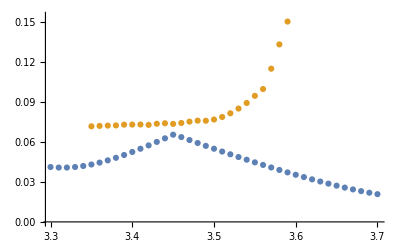

```mathematica
anharmonicboundary2=Import["anhamonicboundary2.dat"];
ListPlot[{boundary2,anharmonicboundary2}]
```

{69.0173,Null}

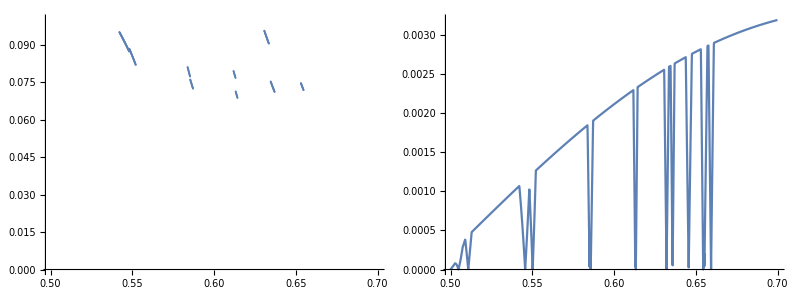

{0,68,87,98,105,108,111,113,114,117,119,122,125,129,132}

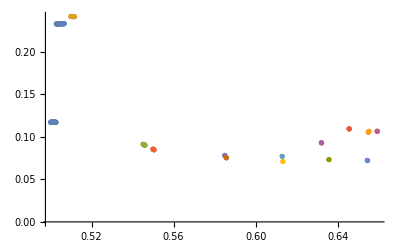

{{0.50811,0.51351},{0.54411,0.54711},{0.54931,0.55111},{0.58471,0.58531},{0.58541,0.58601},{0.61281,0.61311},{0.61331,0.61331},{0.63181,0.63241},{0.63561,0.63591},{0.64531,0.64591},{0.65421,0.65481},{0.65451,0.65571},{0.65901,0.65961}}

{1.69222,Null}

boundary3.dat

Divide::indet: Indeterminate expression 0./0. encountered.

ParallelTable::iterb: Iterator {ϵ,0.61331,0.61331,0.} does not have appropriate bounds.

ParallelTable::nopar1: ParallelTable[{ϵ,f[ϵ,ω]},{ϵ,0.61331,0.61331,0.}] cannot be parallelized; proceeding with sequential evaluation.

Divide::indet: Indeterminate expression 0./0. encountered.

Table::iterb: Iterator {ϵ,0.61331,0.61331,0.} does not have appropriate bounds.

MinimalBy::arg1: The first argument is expected to be a list or association.

Set::shape: Lists {ϵmid,val} and Table[{ϵ,f[ϵ,ω]},{ϵ,0.61331,0.61331,0.}] are not the same shape.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

ParallelTable::iterb: Iterator {ϵ,0.61331,0.61331,0.} does not have appropriate bounds.

ParallelTable::nopar1: ParallelTable[{ϵ,f[ϵ,ω]},{ϵ,0.61331,0.61331,0.}] cannot be parallelized; proceeding with sequential evaluation.

Table::iterb: Iterator {ϵ,0.61331,0.61331,0.} does not have appropriate bounds.

MinimalBy::arg1: The first argument is expected to be a list or association.

Set::shape: Lists {ϵmid,val} and Table[{ϵ,f[ϵ,ω]},{ϵ,0.61331,0.61331,0.}] are not the same shape.

{674.476,Null}

anhamonicboundary3.dat

```mathematica
Δ=0.35;
ω=3.5;
lengths=Δ/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
AbsoluteTiming[vals=ParallelTable[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,lengths],mat2[ω]}];{eval,evec}=First@MinimalBy[DeleteCases[Transpose[{evals,evecs}],u_/;u[[1]]==ComplexInfinity],Abs[Im[#[[1]]]]&];
{ϵ,Re[eval],Im[eval],evec},{ϵ,0.50001,0.7,0.0001}];]
Grid[{{ListPlot[Abs[vals[[All,{1,2}]]],ImageSize->300,PlotRange->{0,0.1}],ListPlot[Abs[vals[[All,{1,3}]]],ImageSize->300,Joined->True,PlotRange->All]}}]
spikes=Cases[vals,u_/;Abs[u[[3]]]<0.0002][[All]];
ends=Join[{0},First/@Position[Differences[spikes[[All,1]]],u_/;u>0.0002],{Length[spikes]}]
ListPlot[Table[{#[[1]],Abs[#[[2]]]}&/@spikes[[ends[[i]]+1;;ends[[i+1]],{1,2}]],{i,1,Length[ends]-1}],PlotRange->All]
ϵranges={2*Min[#]-Max[#],2*Max[#]-Min[#]}&/@Table[#[[1]]&/@spikes[[ends[[i]]+1;;ends[[i+1]],{1,2}]],{i,2,Length[ends]-1}]

AbsoluteTiming[boundary3=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}];]
Export["boundary3.dat",boundary3]
f[ϵ_?NumericQ,ω_?NumericQ]:=Module[{evals,evecs,eval,evec},{evals,evecs}=Eigensystem[{mat1[ϵ,ω,lengths],mat2[ω]}];{eval,evec}=First@MinimalBy[DeleteCases[Transpose[{evals,evecs}],u_/;u[[1]]==ComplexInfinity||Im[u[[1]]]<0],Abs[Im[#[[1]]]]&];
eval]
AbsoluteTiming[Monitor[boundaries=Table[SortBy[Join[ϵmin=ϵranges[[i,1]];
ϵmax=ϵranges[[i,2]];Table[vals=ParallelTable[{ϵ,f[ϵ,ω]},{ϵ,ϵmin,ϵmax,(ϵmax-ϵmin)/16}];
{ϵmid,val}=First@MinimalBy[vals,Im[#[[2]]]&];
ϵmin=ϵmid-0.0025;
ϵmax=ϵmid+0.0025;
{ω, ϵmid,Abs[Re[val]]},{ω,3.5,3.35,-0.01}],ϵmin=ϵranges[[i,1]];
ϵmax=ϵranges[[i,2]];Table[vals=ParallelTable[{ϵ,f[ϵ,ω]},{ϵ,ϵmin,ϵmax,(ϵmax-ϵmin)/16}];
{ϵmid,val}=First@MinimalBy[vals,Im[#[[2]]]&];
ϵmin=ϵmid-0.0025;
ϵmax=ϵmid+0.0025;
{ω, ϵmid,Abs[Re[val]]},{ω,3.5,3.8,0.01}]],#[[1]]&],{i,1,Length[ϵranges]}];,{i,ω}]]
anharmonicboundary3=Table[First@MinimalBy[Cases[Flatten[boundaries,1],u_/;u[[1]]==ω],#[[3]]&],{ω,3.35,3.8,0.01}][[All,{1,3}]];
Export["anharmonicboundary3.dat",anharmonicboundary3]
```

{1.68692,Null}

boundary1.dat

{1.745,Null}

boundary2.dat

{1.68557,Null}

boundary3.dat

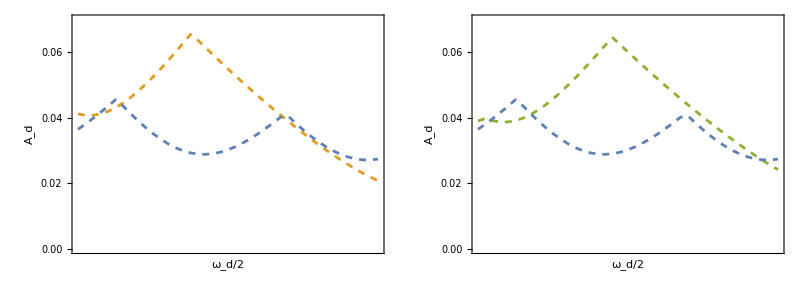

```mathematica
Δ=0.35;
lengths=ConstantArray[0,M];
AbsoluteTiming[boundary1=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}];]
Export["boundary1.dat",boundary1]
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
AbsoluteTiming[boundary2=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}];]
Export["boundary2.dat",boundary2]
lengths=Δ/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
AbsoluteTiming[boundary3=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}];]
Export["boundary3.dat",boundary3]
Grid[{{Show[ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary2,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],PlotRange->{{ωmin,ωmax},{0,0.07}},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],Dashed,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript["ω",d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.0,0.25}],Table[{i,""},{i,1.5,4.5,0.25}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]],Axes->False,Frame->True],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]],Show[ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Cases[boundary3,u_/;u[[1]]==ω],{ω,ωmin,ωmax,0.01}],PlotRange->{{ωmin,ωmax},{0,0.07}},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[3]],Dashed,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript["ω",d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.0,0.25}],Table[{i,""},{i,1.5,4.5,0.25}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]],Axes->False,Frame->True],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[2]]]]}}]
```

```mathematica
(NIntegrate[Interpolation[Table[First@MinimalBy[Join[Cases[boundary2,u_/;u[[1]]==ω],Cases[boundary2,u_/;u[[1]]==ω]],#[[2]]&],{ω,ωmin,ωmax,0.01}]][x],{x,ωmin,ωmax}]-NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}])/NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}]
(NIntegrate[Interpolation[Table[First@MinimalBy[Join[Cases[boundary3,u_/;u[[1]]==ω],Cases[boundary3,u_/;u[[1]]==ω]],#[[2]]&],{ω,ωmin,ωmax,0.01}]][x],{x,ωmin,ωmax}]-NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}])/NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}]
```

0.249181

0.267103

```mathematica
AbsoluteTiming[Monitor[Do[Δ=0.5;
lengths=Flatten[Import["data/randomlengths/randomlengths"<>ToString[n]<>".dat"]];
boundary=ParallelTable[Quiet[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}]];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,3.0,3.9,0.05}];
Export["data/randomlengths/boundary"<>ToString[n]<>".dat",boundary];,{n,1,10}],{n, i,ω,time}]]
```

{11.5966,Null}

```mathematica
AbsoluteTiming[Monitor[Do[Δ=0.5;
lengths=Flatten[Import["data/randomlengths/randomlengths"<>ToString[n]<>".dat"]];
ω=3.5;
time=AbsoluteTiming[vals=ParallelTable[Quiet[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,lengths],mat2[ω]}]];{eval,evec}=First@MinimalBy[DeleteCases[Transpose[{evals,evecs}],u_/;u[[1]]==ComplexInfinity],Abs[Im[#[[1]]]]&];
{ϵ,Re[eval],Im[eval],evec},{ϵ,0.5001,0.7,0.0001}];];
spikes=Cases[vals,u_/;Abs[u[[3]]]<0.0002][[All]];
ends=Join[{0},First/@Position[Differences[spikes[[All,1]]],u_/;u>0.0002],{Length[spikes]}];
ϵranges={2*Min[#]-Max[#],2*Max[#]-Min[#]}&/@Table[#[[1]]&/@spikes[[ends[[i]]+1;;ends[[i+1]],{1,2}]],{i,2,Length[ends]-1}];
boundary=ParallelTable[Quiet[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}]];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,3.35,3.7,0.05}];
Export["data/randomlengths/boundary"<>ToString[n]<>".dat",boundary];
f[ϵ_?NumericQ,ω_?NumericQ]:=Module[{evals,evecs,eval,evec},Quiet[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,lengths],mat2[ω]}]];{eval,evec}=First@MinimalBy[DeleteCases[Transpose[{evals,evecs}],u_/;u[[1]]==ComplexInfinity||Im[u[[1]]]<0],Abs[Im[#[[1]]]]&];
eval];
boundaries=Table[SortBy[Join[ϵmin=ϵranges[[i,1]];
ϵmax=ϵranges[[i,2]];Table[vals=ParallelTable[{ϵ,f[ϵ,ω]},{ϵ,ϵmin,ϵmax,(ϵmax-ϵmin)/16}];
{ϵmid,val}=First@MinimalBy[vals,Im[#[[2]]]&];
ϵmin=ϵmid-0.0025;
ϵmax=ϵmid+0.0025;
{ω, ϵmid,Abs[Re[val]]},{ω,3.5,3.35,-0.01}],ϵmin=ϵranges[[i,1]];
ϵmax=ϵranges[[i,2]];Table[vals=ParallelTable[{ϵ,f[ϵ,ω]},{ϵ,ϵmin,ϵmax,(ϵmax-ϵmin)/16}];
{ϵmid,val}=First@MinimalBy[vals,Im[#[[2]]]&];
ϵmin=ϵmid-0.0025;
ϵmax=ϵmid+0.0025;
{ω, ϵmid,Abs[Re[val]]},{ω,3.5,3.7,0.05}]],#[[1]]&],{i,1,Length[ϵranges]}];
anharmonicboundary=Table[First@MinimalBy[Cases[Flatten[boundaries,1],u_/;u[[1]]==ω],#[[3]]&],{ω,3.35,3.7,0.05}][[All,{1,3}]];
Export["data/randomlengths/anhamonicboundary"<>ToString[n]<>".dat",anharmonicboundary];,{n,1,10}],{n, i,ω,time}]]
```

```mathematica
{plots,vals}=Transpose[Table[boundary=Import["data/randomlengths/boundary"<>ToString[n]<>".dat"];
anharmonicboundary=Import["data/randomlengths/anhamonicboundary"<>ToString[n]<>".dat"];
tongues=Import["data/randomlengths/tongues"<>ToString[n]<>".dat"];
{Show[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues}],InterpolationOrder->0,PlotRange->{All,All,{0.45,0.6}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-0.45)/(0.6-0.45)]&),ColorFunctionScaling->False, FrameLabel->{{None,None},{Subscript["ω",d],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i,{3,2}]},{i,3,4.0,0.5}],Table[{i,""},{i,3,4,0.5}]}},RotateLabel->False,AspectRatio->1,ImagePadding->{{65,15},{65,10}},PlotLegends->True],ListPlot[Table[First@MinimalBy[Join[Cases[boundary,u_/;u[[1]]==ω],Cases[anharmonicboundary,u_/;u[[1]]==ω]],#[[2]]&],{ω,ωmin,ωmax,0.05}],Joined->True,PlotStyle->Directive[Black,Dashed]]],NIntegrate[Interpolation[Table[First@MinimalBy[Join[Cases[boundary,u_/;u[[1]]==ω],Cases[anharmonicboundary,u_/;u[[1]]==ω]],#[[2]]&],{ω,ωmin,ωmax,0.05}]][x],{x,ωmin,ωmax}]},{n,1,10}]];
```

```mathematica
Δ=0.0;
lengths=ConstantArray[0,M];
AbsoluteTiming[boundary1=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}];]
Export["boundary1.dat",boundary1]

Δ=0.5;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
AbsoluteTiming[boundary2=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}];]
Export["boundary2.dat",boundary2]

lengths=Flatten[Import["data/randomlengths.dat"]];
AbsoluteTiming[boundary3=ParallelTable[{evals,evecs}=Eigensystem[{mat1[1/2,ω,lengths],mat2[ω]}];
{ω,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,(ωmax-ωmin)/Npoints}];]
Export["boundary3.dat",boundary3]
```

{6.69875,Null}

boundary1.dat

{6.86841,Null}

boundary2.dat

{6.74898,Null}

boundary3.dat

## Anharmonic eigenvalues

```mathematica
mat1[s_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(s+n)^2+I*ω*η*(s+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+Exp[I*q]*KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(Exp[-I*q]*KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
mat2[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
```

{0.447342,Null}

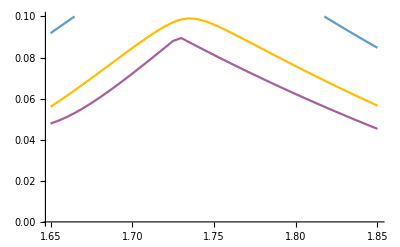

3.4

{19.6536,Null}

{19.0092,Null}

{19.736,Null}

-Graphics-

```mathematica
AbsoluteTiming[Monitor[boundary=Table[ParallelTable[{evals,evecs}=Eigensystem[{mat1[0.5,ω,0.5,q],mat2[ω]}];
{ω/2,Min[Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]]]},{ω,ωmin,ωmax,0.01}],{q,0,Pi,Pi/8}];,N[q/(Pi)]]]
ListPlot[boundary,Joined->True,PlotRange->{0,0.1}]
ω=3.4
dϵ=0.0001;
Monitor[AbsoluteTiming[vals1=Table[Transpose[ParallelTable[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,0.0,q],mat2[ω]},-4];
Transpose[{Im[SortBy[evals,Im[#]&]],Abs[Re[SortBy[evals,Im[#]&]]]}],{ϵ,0,1,dϵ}]],{q,0,Pi,Pi/8}];],N[q/Pi]]
Monitor[AbsoluteTiming[vals2=Table[Transpose[ParallelTable[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,0.25,q],mat2[ω]},-4];
Transpose[{Im[SortBy[evals,Im[#]&]],Abs[Re[SortBy[evals,Im[#]&]]]}],{ϵ,0,1,dϵ}]],{q,0,Pi,Pi/8}];],N[q/Pi]]
Monitor[AbsoluteTiming[vals3=Table[Transpose[ParallelTable[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,0.5,q],mat2[ω]},-4];
Transpose[{Im[SortBy[evals,Im[#]&]],Abs[Re[SortBy[evals,Im[#]&]]]}],{ϵ,0,1,dϵ}]],{q,0,Pi,Pi/8}];],N[q/Pi]]
Grid[{{Show@@Table[ListPlot[vals1[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[ColorData[97,"ColorList"][[i]]]],{i,1,Length[vals1]}],Show@@Table[ListPlot[vals2[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[ColorData[97,"ColorList"][[i]]]],{i,1,Length[vals2]}],Show@@Table[ListPlot[vals3[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[ColorData[97,"ColorList"][[i]]]],{i,1,Length[vals3]}]}}]
```

```mathematica
wave={1,2,3,9};Grid[{{Show@@Table[ListPlot[vals1[[wave[[i]]]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[ColorData[97,"ColorList"][[i]]]],{i,1,Length[wave]}],Show@@Table[ListPlot[vals2[[wave[[i]]]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[ColorData[97,"ColorList"][[i]]]],{i,1,Length[wave]}],Show@@Table[ListPlot[vals3[[wave[[i]]]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[ColorData[97,"ColorList"][[i]]]],{i,1,Length[wave]}]}}]
Show@@Table[ListPlot[vals3[[wave[[i]]]],PlotRange->{{-0.05,0.05},{0.045,0.055}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[ColorData[97,"ColorList"][[i]]]],{i,1,Length[wave]}]
```

-Graphics-

-Graphics-

```mathematica
ω=3.4
dϵ=0.0001;
Monitor[AbsoluteTiming[vals1=Table[Transpose[ParallelTable[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,0.0,q],mat2[ω]},-4];
Transpose[{Im[SortBy[Cases[evals,u_/;Im[u]>0],Im]],Abs[Re[SortBy[Cases[evals,u_/;Im[u]>0],Im]]]}],{ϵ,0,1,dϵ}]],{q,0,Pi,Pi/2}];],N[q/Pi]]
Monitor[AbsoluteTiming[vals2=Table[Transpose[ParallelTable[{evals,evecs}=Eigensystem[{mat1[ϵ,ω,0.5,q],mat2[ω]},-4];
Transpose[{Im[SortBy[Cases[evals,u_/;Im[u]>0],Im]],Abs[Re[SortBy[Cases[evals,u_/;Im[u]>0],Im]]]}],{ϵ,0,1,dϵ}]],{q,0,Pi,Pi/2}];],N[q/Pi]]
```

3.4

{39.5446,Null}

{39.3265,Null}

```mathematica
Grid[{{Show@@Table[Show[ListPlot[vals1[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black,Dashed]],ListPlot[{-#[[1]],#[[2]]}&/@#&/@vals1[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black,Dashed]]],{i,1,Length[vals1]}],Show@@Table[Show[ListPlot[vals2[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black]],ListPlot[{-#[[1]],#[[2]]}&/@#&/@vals2[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->500,Joined->True,Frame->True,Axes->False,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black]]],{i,1,Length[vals2]}]}}]
```

-Graphics- | -Graphics-

```mathematica
tongues5=Import["tongues5.dat"];
anharmonicboundary5=Import["anharmonicboundary5.dat"];
boundary5=Import["boundary5.dat"];
boundary1=Import["data/boundary1.dat"];
cmin=Min[Cases[tongues5[[All,4]],u_/;u>0.55]];
cmax=Max[Cases[tongues5[[All,4]],u_/;u>0.55]];
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-cmin)/(cmax-cmin)]]
Δ=0.5;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
thetas=RandomReal[{-Pi/16,Pi/16},M];
f[x_]:=lengths[[Round[x]]]
p0=Show[Graphics[{Table[Line[{{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->1000],Plot[1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,2}}],PlotRange->{{1/2,M+1/2},{-1,1.75}}];

Clear[ω]
p1=Show[Block[{Δ=0},ListPlot[{Table[{q,Re[ω/.dispersion[[2]]]},{q,0,Pi,Pi/50}],Table[{q,Re[ω/.dispersion[[4]]]},{q,0,Pi,Pi/50}]},Joined->True,PlotStyle->Directive[AbsoluteThickness[2],Black,Dashed],Axes->False,Frame->True,FrameLabel->{k,"ω"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/2,PlotRange->{1/2,5/2},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.5,2.5,0.5}],Table[{i,""},{i,0.5,2.5,0.5}]},{{{0,0},{π/4,DisplayForm[RowBox[{"π","/",8}]]},{π/2,DisplayForm[RowBox[{"π","/",4}]]},{(3 π)/4,DisplayForm[RowBox[{3"π","/",8}]]},{π,DisplayForm[RowBox[{"π","/",2}]]}},Table[{i,""},{i,0,Pi,Pi/4}]}}]],Block[{Δ=0.5},ListPlot[{Table[{q,Re[ω/.dispersion[[2]]]},{q,0,Pi,Pi/50}],Table[{q,Re[ω/.dispersion[[4]]]},{q,0,Pi,Pi/50}]},Joined->True,PlotStyle->Directive[AbsoluteThickness[2],Black]]],ImageSize->350,ImagePadding->{{65,15},{65,10}},PlotRange->{{0,Pi+0.1},{1,2.5}}];
p2=Grid[{{Show@@Table[Show[ListPlot[vals1[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->350,AspectRatio->1/4,ImagePadding->{{75,5},{10,10}},Joined->True,Frame->True,Axes->False,FrameLabel->{None,Re[λ]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black,AbsoluteThickness[1],Dashed]],ListPlot[{-#[[1]],#[[2]]}&/@#&/@vals1[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->350,AspectRatio->1/4,ImagePadding->{{75,5},{10,10}},Joined->True,Frame->True,Axes->False,FrameLabel->{None,Re[λ]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black,AbsoluteThickness[1],Dashed]]],{i,1,Length[vals1]}]},{Show@@Table[Show[ListPlot[vals2[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->350,AspectRatio->1/4,ImagePadding->{{75,5},{75,10}},Joined->True,Frame->True,Axes->False,FrameLabel->{Im[λ],Re[λ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black,AbsoluteThickness[1]]],ListPlot[{-#[[1]],#[[2]]}&/@#&/@vals2[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->350,AspectRatio->1/4,ImagePadding->{{75,5},{75,10}},Joined->True,Frame->True,Axes->False,FrameLabel->{Im[λ],Re[λ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black,AbsoluteThickness[1]]]],{i,1,Length[vals2]}]}}];
p3=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues5}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript["ω",d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[Black,Dashed,AbsoluteThickness[2]]],ListContourPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues5}],Contours->{0.475},ContourShading->None,ContourStyle->Directive[Black,Opacity[1],AbsoluteThickness[2]],PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript["ω",d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]];
p=Grid[{{p0},{Grid[{{p1,p2,p3}}]}}]
Export["anharmonic.pdf",p]
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

anharmonic.pdf

```mathematica
ListContourPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues5}],Contours->{0.475},ContourShading->None,ContourStyle->Directive[Black,Opacity[1],AbsoluteThickness[2]],PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript["ω",d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,ωmin,ωmax,0.2}],Table[{i,""},{i,ωmin,ωmax,0.2}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

-Graphics-

```mathematica
cmin
cmax
```

0.56

0.7

```mathematica
{Table[{i,""},{i,cmin,cmax,(cmax-cmin)/5/5}],Table[{i,PaddedForm[i,{3,2}]},{i,cmin,cmax,(cmax-cmin)/5}]}
```

```mathematica
p=BarLegend[{cf[#]&,{cmin,cmax}},LegendLabel->DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],LabelStyle->Directive[12,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->{50,100},Ticks->{{1, 2}, {Table[{i,i},{i,cmin,cmax,(cmax-cmin)/5/5}],Table[{i,PaddedForm[i,{3,2}]},{i,cmin,cmax,(cmax-cmin)/5}]}}]
Export["colorbar.pdf",p]
```

colorbar.pdf

```mathematica
p2=Grid[{{Show@@Table[ListPlot[vals1[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->350,AspectRatio->1/4,ImagePadding->{{75,5},{10,10}},Joined->True,Frame->True,Axes->False,FrameLabel->{None,Re[λ]},FrameTicks->{{Automatic,Automatic},{None,Automatic}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black,AbsoluteThickness[1],Dashed]],{i,1,Length[vals1],2}]},{Show@@Table[ListPlot[vals3[[i]],PlotRange->{{-0.5,0.5},{0,0.4}},ImageSize->350,AspectRatio->1/4,ImagePadding->{{75,5},{75,10}},Joined->True,Frame->True,Axes->False,FrameLabel->{Im[λ],Re[λ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[Black,AbsoluteThickness[1]]],{i,1,Length[vals3],3}]}}]
Export["test.pdf",p2]
```

-Graphics-
-Graphics-

test.pdf

## Plots

```mathematica
tongues1=Import["data/tongues1.dat"];
tongues2=Import["data/tongues2.dat"];
tongues3=Import["data/tongues3.dat"];
boundary1=Import["data/boundary1.dat"];
boundary2=Import["data/boundary2.dat"];
boundary3=Import["data/boundary3.dat"];
anharmonicboundary2=Import["data/anharmonicboundary2.dat"];
anharmonicboundary3=Import["data/anharmonicboundary3.dat"];
frequencies1=Flatten[Import["data/frequencies1.dat"]];
frequencies2=Flatten[Import["data/frequencies2.dat"]];
frequencies3=Flatten[Import["data/frequencies3.dat"]];
```

```mathematica
(NIntegrate[Interpolation[Table[First@MinimalBy[Join[Cases[boundary2,u_/;u[[1]]==ω],Cases[anharmonicboundary2,u_/;u[[1]]==ω]],#[[2]]&],{ω,ωmin,ωmax,0.01}]][x],{x,ωmin,ωmax}]-NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}])/NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}]
(NIntegrate[Interpolation[Table[First@MinimalBy[Join[Cases[boundary3,u_/;u[[1]]==ω],Cases[anharmonicboundary3,u_/;u[[1]]==ω]],#[[2]]&],{ω,ωmin,ωmax,0.01}]][x],{x,ωmin,ωmax}]-NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}])/NIntegrate[Interpolation[boundary1][x],{x,ωmin,ωmax}]
```

0.287035

0.30352

```mathematica
Clear[ω];
p0=Show[Block[{Δ=0},ListPlot[{Table[{q,Re[ω/.dispersion[[2]]]},{q,0,Pi,Pi/50}],Table[{q,Re[ω/.dispersion[[4]]]},{q,0,Pi,Pi/50}]},Joined->True,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->True,FrameLabel->{k,ω},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/2,PlotRange->{1/2,5/2},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.5,2.5,0.5}],Table[{i,""},{i,0.5,2.5,0.5}]},{{{0,0},{π/4,DisplayForm[RowBox[{"π","/",8}]]},{π/2,DisplayForm[RowBox[{"π","/",4}]]},{(3 π)/4,DisplayForm[RowBox[{3"π","/",8}]]},{π,DisplayForm[RowBox[{"π","/",2}]]}},Table[{i,""},{i,0,Pi,Pi/4}]}}]],Block[{Δ=0.35},ListPlot[{Table[{q,Re[ω/.dispersion[[2]]]},{q,0,Pi,Pi/50}],Table[{q,Re[ω/.dispersion[[4]]]},{q,0,Pi,Pi/50}]},Joined->True,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]]],

ListPlot[Table[{Pi/(M/2)*(i-1),Reverse[frequencies1][[i]]},{i,1,M/2+1,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]]],
ListPlot[Table[{Pi/(M/2)*(i+1),Reverse[frequencies1][[i+1]]},{i,1,M/2,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]]],
ListPlot[Table[{Pi/(M/2)*(M-i),Reverse[frequencies1][[i]]},{i,M/2,M,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]]],ListPlot[Table[{Pi/(M/2)*(M-i),Reverse[frequencies1][[i+1]]},{i,M/2,M-1,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]]],

ListPlot[Table[{Pi/(M/2)*(i-1),Reverse[frequencies2][[i]]},{i,1,M/2+1,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],
ListPlot[Table[{Pi/(M/2)*(i+1),Reverse[frequencies2][[i+1]]},{i,1,M/2,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],
ListPlot[Table[{Pi/(M/2)*(M-i),Reverse[frequencies2][[i]]},{i,M/2,M,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],ListPlot[Table[{Pi/(M/2)*(M-i),Reverse[frequencies2][[i+1]]},{i,M/2,M-1,2}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],

ListPlot[Join[Table[{Pi/(M/2)*(i-1),Reverse[frequencies3][[i]]},{i,1,M/2-1,2}],{{Pi,Reverse[frequencies3][[M/2]]}}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[3]]],Joined->False],
ListPlot[Join[{{0,Reverse[frequencies3][[1]]}},Table[{Pi/(M/2)*(i+1),Reverse[frequencies3][[i+1]]},{i,1,M/2,2}]],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[3]]],Joined->False],
ListPlot[Join[{{Pi,Reverse[frequencies3][[1+M/2]]}},Table[{Pi/(M/2)*(M-i),Reverse[frequencies3][[i]]},{i,M/2+2,M,2}]],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[3]]],Joined->False],
ListPlot[Join[Table[{Pi/(M/2)*(M-i),Reverse[frequencies3][[i+1]]},{i,M/2,M-1,2}],{{0,Reverse[frequencies3][[M]]}}],PlotRange->All,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[3]]],Joined->False],

ListPlot[Join[Table[{Pi/(M/2)*(i-1),Reverse[frequencies3][[i]]},{i,1,M/2-1,2}],{{Pi,Reverse[frequencies3][[M/2]]}}],PlotRange->All,PlotStyle->Directive[PointSize[0.02],ColorData[97,"ColorList"][[3]]],Joined->True,InterpolationOrder->5],
ListPlot[Join[{{0,Reverse[frequencies3][[1]]}},Table[{Pi/(M/2)*(i+1),Reverse[frequencies3][[i+1]]},{i,1,M/2,2}]],PlotRange->All,PlotStyle->Directive[PointSize[0.02],ColorData[97,"ColorList"][[3]]],Joined->True,InterpolationOrder->5],
ListPlot[Join[{{Pi,Reverse[frequencies3][[1+M/2]]}},Table[{Pi/(M/2)*(M-i),Reverse[frequencies3][[i]]},{i,M/2+2,M,2}]],PlotRange->All,PlotStyle->Directive[PointSize[0.02],ColorData[97,"ColorList"][[3]]],Joined->True,InterpolationOrder->5],ListPlot[Join[Table[{Pi/(M/2)*(M-i),Reverse[frequencies3][[i+1]]},{i,M/2,M-1,2}],{{0,Reverse[frequencies3][[M]]}}],PlotRange->All,PlotStyle->Directive[PointSize[0.02],ColorData[97,"ColorList"][[3]]],Joined->True,InterpolationOrder->5],ImageSize->350,ImagePadding->{{65,15},{65,10}},PlotRange->{{0,Pi+0.1},{1,2.5}}];

p5=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues2}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.0,0.25}],Table[{i,""},{i,1.5,4.5,0.25}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Join[Cases[boundary2,u_/;u[[1]]==ω],Cases[anharmonicboundary2,u_/;u[[1]]==ω]],{ω,ωmin,ωmax,0.01}],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[3]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[3]]]];
p6=Show[rasterizeBackground[ListDensityPlot[Table[If[val[[5]]>0,{val[[3]],val[[2]],val[[4]]},{val[[3]],val[[2]],-1}],{val,tongues3}],InterpolationOrder->1,PlotRange->{All,All,{0.45,0.7}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->cf,ColorFunctionScaling->False, FrameLabel->{{Subscript[A,d],None},{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None}},ImageSize->350,FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.1,0.02}],Table[{i,""},{i,0,0.1,0.02}]},{Table[{i,PaddedForm[i/2,{3,2}]},{i,1.5,4.0,0.25}],Table[{i,""},{i,1.5,4.5,0.25}]}},RotateLabel->True,AspectRatio->1/2,ImagePadding->{{65,15},{65,10}},FrameStyle->Directive[Black,AbsoluteThickness[2]]]],ListPlot[Table[First@(MinimalBy[#,#[[2]]&])&@Join[Cases[boundary3,u_/;u[[1]]==ω],Cases[anharmonicboundary3,u_/;u[[1]]==ω]],{ω,ωmin,ωmax,0.01}],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[3]]],ListPlot[boundary1,Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed,AbsoluteThickness[3]]]];
p3=Legended[Grid[{{p0,p5,p6}}],Placed[BarLegend[{cf[#]&,{0.45,0.7}},LegendLabel->DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],LabelStyle->Directive[12,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->{50,100}],Right]]
p3=Grid[{{p0,p5,p6}}]
```

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics-

```mathematica
lengths=ConstantArray[0,M];
thetas=RandomReal[{-Pi/16,Pi/16},M];
fourier=Fourier[lengths];
f[x_]=Re[Sum[fourier[[i]]*Exp[-2*Pi*I*(i-1)*(x-1)/M],{i,1,M}]/(M)^(1/2)];
p0=Show[Graphics[{Table[Line[{{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->1000],Plot[1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,2}}],PlotRange->{{1/2,M+1/2},{-1,1.75}}];
Δ=0.35;
lengths=Riffle[ConstantArray[Δ,M/2],ConstantArray[-Δ,M/2]];
thetas=RandomReal[{-Pi/16,Pi/16},M];
fourier=Fourier[lengths];
f[x_]=Re[Sum[fourier[[i]]*Exp[-2*Pi*I*(i-1)*(x-1)/M],{i,1,M}]/(M)^(1/2)];
f[x_]:=lengths[[Round[x]]]
p1=Show[Graphics[{Table[Line[{{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->1000],Plot[1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,2}}],PlotRange->{{1/2,M+1/2},{-1,1.75}}];

lengths=0.35/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
thetas=RandomReal[{-Pi/16,Pi/16},M];
fourier=Fourier[lengths];
f[x_]=Re[Sum[fourier[[i]]*Exp[-2*Pi*I*(i-1)*(x-1)/M],{i,1,M}]/(M)^(1/2)];
f[x_]:=lengths[[Round[x]]]
p2=Show[Graphics[{Table[Line[{{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->1000],Plot[1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,2}}],PlotRange->{{1/2,M+1/2},{-1,1.75}}];
p=Grid[{{p0},{p1},{p2},{p3}}]
Export["fig2.pdf",p]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics- | -Graphics-

fig2.pdf

## Animation

```mathematica
κ=1;
η=0.1;
M=32;
γ=0.05;
ω=3.5;
tmax=2*Pi*500;
t1=2*Pi*450;
dt=2*Pi*0.05;
Clear[Δ]
Clear[lengths]
Δ[i_]:=lengths[[Mod[i-1,M]+1]];
pbcs={θ[0]->θ[M],θ[M+1]->θ[1]};
ics=Join[Table[θ[i][0]==RandomReal[{-10^-1,10^-1}],{i,1,M}],Table[θ[i]'[0]==0,{i,1,M}]];
eqns:=Table[0==(1+2 κ (1+Δ[i])-γ ω^2 Cos[t]) Sin[θ[i][t]]-κ (Sin[θ[-1+i][t]-θ[i][t]]+Sin[θ[i][t]]) (1+Δ[-1+i])-κ (Sin[θ[1+i][t]-θ[i][t]]+Sin[θ[i][t]]) (1+Δ[1+i])+(1+Δ[i]) (η ω θ[i]'[t]+ω^2 θ[i]''[t])/.pbcs,{i,1,M}];

lengths=Riffle[ConstantArray[0.0,M/2],ConstantArray[0.0,M/2]];
sol1=NDSolve[{eqns,ics},Table[θ[i],{i,1,M}],{t,0,tmax}];
norms=Table[Sum[Abs[θ[i][t]]^2,{i,1,M}]/M/.sol1[[1]],{t,0,tmax,dt}];
Grid[{{ListPlot[Log[norms],Joined->True,ImageSize->300],ListPlot[{Table[{t,θ[1][t]/.sol1[[1]]},{t,t1,tmax,dt}],Table[{t,Cos[t]},{t,t1,tmax,dt}]},Joined->True,ImageSize->300]}}]

lengths=Riffle[ConstantArray[0.35,M/2],ConstantArray[-0.35,M/2]];
sol2=NDSolve[{eqns,ics},Table[θ[i],{i,1,M}],{t,0,tmax}];
norms=Table[Sum[Abs[θ[i][t]]^2,{i,1,M}]/M/.sol2[[1]],{t,0,tmax,dt}];
Grid[{{ListPlot[Log[norms],Joined->True,ImageSize->300],ListPlot[{Table[{t,θ[1][t]/.sol2[[1]]},{t,t1,tmax,dt}],Table[{t,Cos[t]},{t,t1,tmax,dt}]},Joined->True,ImageSize->300]}}]

lengths=0.35/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
sol3=NDSolve[{eqns,ics},Table[θ[i],{i,1,M}],{t,0,tmax}];
norms=Table[Sum[Abs[θ[i][t]]^2,{i,1,M}]/M/.sol3[[1]],{t,0,tmax,dt}];
Grid[{{ListPlot[Log[norms],Joined->True,ImageSize->300],ListPlot[{Table[{t,θ[1][t]/.sol3[[1]]},{t,t1,tmax,dt}],Table[{t,Cos[t]},{t,t1,tmax,dt}]},Joined->True,ImageSize->300]}}]
```

-Graphics- | -Graphics-

-Graphics- | -Graphics-

-Graphics- | -Graphics-

```mathematica
t1=2*Pi*450;
dt=2*Pi*0.05;
AbsoluteTiming[plots=ParallelTable[
lengths=ConstantArray[0,M];
thetas=Table[θ[i][t]/.sol1[[1]],{i,1,M}];
f[x_]:=lengths[[Round[x]]];
z0={0,γ*Cos[t]};
p0=Show[Graphics[{Table[Line[{z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->2000,PlotRange->{{1/2,M+1/2},{-1,1.75}+z0[[2]]}],Plot[z0[[2]]+1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,1.75}+z0[[2]]}],PlotRange->{{1/2,M+1/2},{-1,2}}];
lengths=Riffle[ConstantArray[0.35,M/2],ConstantArray[-0.35,M/2]];
thetas=Table[θ[i][t]/.sol2[[1]],{i,1,M}];
f[x_]:=lengths[[Round[x]]];
p1=Show[Graphics[{Table[Line[{z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->2000,PlotRange->{{1/2,M+1/2},{-1,1.75}+z0[[2]]}],Plot[z0[[2]]+1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,1.75}+z0[[2]]}],PlotRange->{{1/2,M+1/2},{-1,2}}];
lengths=0.35/0.5*Flatten[Import["data/randomlengths/randomlengths"<>ToString[10]<>".dat"]];
thetas=Table[θ[i][t]/.sol3[[1]],{i,1,M}];
f[x_]:=lengths[[Round[x]]];
p2=Show[Graphics[{Table[Line[{z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{i+1,1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{M+1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{1,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[z0+{i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->2000,PlotRange->{{1/2,M+1/2},{-1,1.75}+z0[[2]]}],Plot[z0[[2]]+1+f[x],{x,1/2,M+1/2},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Axes->False,Frame->False,Filling->Top,FillingStyle->Directive[Opacity[1]],PlotRange->{{1/2,M+1/2},{-1,1.75}+z0[[2]]}],PlotRange->{{1/2,M+1/2},{-1,2}}];Grid[{{p0},{p1},{p2}}],{t,t1,tmax,dt}];]
```

{61.4466,Null}

```mathematica
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦773⟧ is longer than depth of object.

```mathematica
AbsoluteTiming[Monitor[Do[Export["animation/"<>IntegerString[i,10,4]<>".png",plots[[i]]];,{i,1,Length[plots]}],N[i/Length[plots]]]]
```

{276.354,Null}